```mathematica
A=15.85; B=18.34; c=0.71; d=23.21; F=12;p=1;

A-B*(y+x)^(-1/3)-c*(y*(y-1)/((y+x)^(4/3)))-d*((x-2*y)^2)/((y+x)^2)-(F/(y+x)^(5/2))*(Mod[x,2]+Mod[y,2]-1)
```

15.85-(23.21 (x-2 y)^2)/(x+y)^2-(0.71 (-1+y) y)/(x+y)^(4/3)-18.34/(x+y)^(1/3)-(12 (-1+Mod[x,2]+Mod[y,2]))/(x+y)^(5/2)

```mathematica
f[x_,y_]:=15.85-(23.21 (x-2 y)^2)/(x+y)^2-(0.71 (-1+y) y)/(x+y)^(4/3)-18.34/(x+y)^(1/3)-(12 (-1+Mod[x,2]+Mod[y,2]))/(x+y)^(5/2)
```

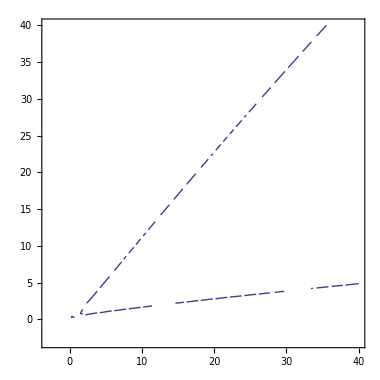

```mathematica
ContourPlot[{f[x,y]==0},{x,-3,40},{y,-3,40}]
```

```mathematica
Dt[f[x,y],x]
```

-(46.42 (x-2 y) (1-2 Dt[y,x]))/(x+y)^2-(0.71 (-1+y) Dt[y,x])/(x+y)^(4/3)-(0.71 y Dt[y,x])/(x+y)^(4/3)+(46.42 (x-2 y)^2 (1+Dt[y,x]))/(x+y)^3+(0.946667 (-1+y) y (1+Dt[y,x]))/(x+y)^(7/3)+(6.11333 (1+Dt[y,x]))/(x+y)^(4/3)+(30 (1+Dt[y,x]) (-1+Mod[x,2]+Mod[y,2]))/(x+y)^(7/2)-(12 (Mod^(1,0)[x,2]+Dt[y,x] Mod^(1,0)[y,2]))/(x+y)^(5/2)

```mathematica
fff[x_,y_,z_]:=-(46.42(x-2 y) (1-2 z))/(x+y)^2-(0.71 (-1+y)z)/(x+y)^(4/3)-(0.71y z)/(x+y)^(4/3)+(46.42 (x-2 y)^2 (1+z))/(x+y)^3+(0.9466666666666665 (-1+y) y (1+z))/(x+y)^(7/3)+(6.113333333333333 (1+z))/(x+y)^(4/3)+(30 (1+z) (-1+Mod[x,2]+Mod[y,2]))/(x+y)^(7/2)-(12 (Derivative[1,0][Mod][x,2]+z Derivative[1,0][Mod][y,2]))/(x+y)^(5/2)
```

3.475063393859375*^9}, {

   3.47506371478125*^9, 3.475063774828125*^9}, {3.475063825859375*^9, 

   3.47506383825*^9}, 3.475068303125*^9}],



Cell[BoxData[""], "Input",

 CellChangeTimes->{{3.475068300359375*^9, 3.475068300390625*^9}}],



Cell[BoxData[""], "Input",

 CellChangeTimes->{{3.475063511578125*^9, 3.475063514578125*^9}, 

   3.475063846234375*^9}],



Cell[CellGroupData[{



Cell[BoxData[{

 RowBox[{

  RowBox[{

   RowBox[{"A", "=", "15.85"}], ";", " ", 

   RowBox[{"B", "=", "18.34"}], ";", " ", 

   RowBox[{"c", "=", "0.71"}], ";", " ", 

   RowBox[{"d", "=", "23.21"}], ";", " ", 

   RowBox[{"F", "=", "12"}], ";", 

   RowBox[{"p", "=", "1"}], ";"}], 

  "\[IndentingNewLine]"}], "\[IndentingNewLine]", 

 RowBox[{"A", "-", 

  RowBox[{"B", "*", 

   RowBox[{

    RowBox[{"(", 

     RowBox[{"y", "+", "x"}], ")"}], "^", 

    RowBox[{"(", 

     RowBox[{

      RowBox[{"-", "1"}], "/", "3"}], ")"}]}]}], "-", 

  RowBox[{"c", "*", 

   RowBox[{"(", 

    RowBox[{"y", "*", 

     RowBox[{

      RowBox[{"(", 

       RowBox[{"y", "-", "1"}], ")"}], "/", 

      RowBox[{"(", 

       RowBox[{

        RowBox[{"(", 

         RowBox[{"y", "+", "x"}], ")"}], "^", 

        RowBox[{"(", 

         RowBox[{"4", "/", "3"}], ")"}]}], ")"}]}]}], ")"}]}], "-", 

  RowBox[{"d", "*", 

   RowBox[{

    RowBox[{"(", 

     RowBox[{

      RowBox[{"(", 

       RowBox[{"x", "-", 

        RowBox[{"2", "*", "y"}]}], ")"}], "^", "2"}], ")"}], "/", 

    RowBox[{"(", 

     RowBox[{

      RowBox[{"(", 

       RowBox[{"y", "+", "x"}], ")"}], "^", "2"}], ")"}]}]}], "-", 

  RowBox[{

   RowBox[{"(", 

    RowBox[{"F", "/", 

     RowBox[{

      RowBox[{"(", 

       RowBox[{"y", "+", "x"}], ")"}], "^", 

      RowBox[{"(", 

       RowBox[{"5", "/", "2"}], ")"}]}]}], ")"}], "*", 

   RowBox[{"(", 

    RowBox[{

     RowBox[{"Mod", "[", 

      RowBox[{"x", ",", "2"}], "]"}], "+", 

     RowBox[{"Mod", "[", 

      RowBox[{"y", ",", "2"}], "]"}], "-", "1"}], ")"}]}]}]}], "Input",

 CellChangeTimes->{{3.47506343609375*^9, 3.475063456703125*^9}, {

   3.475063516609375*^9, 3.47506351790625*^9}, 3.475063637109375*^9, {

   3.475063679515625*^9, 3.475063686296875*^9}}],



Cell[BoxData[

 RowBox[{"15.85`", "\[InvisibleSpace]", "-", 

  FractionBox[

   RowBox[{"23.21`", " ", 

    SuperscriptBox[

     RowBox[{"(", 

      RowBox[{"x", "-", 

       RowBox[{

```mathematica
FindRoot[f[20,y],{y,22}]
```

{y→22.7467}

```mathematica
FindRoot[f[20,y],{y,2}]
```

{y→2.77975}

```mathematica
FindRoot[fff[22,22.7467,z],{z,1}]
```

{z→1.11149}

```mathematica
FindRoot[fff[22,2.77975,z],{z,0.1}]
```

{z→0.0151444}

```mathematica
M=1.1114857652231187; m =0.015144373698252389;
```

```mathematica
prom=(M+m)/2
```

0.563315

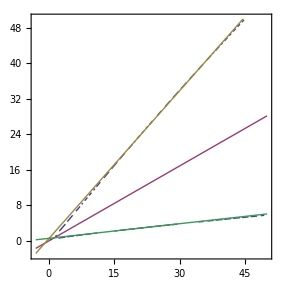

```mathematica
ContourPlot[{f[x,y]==0,prom*(x)-y==0, M*(x-20)-(y-22.7467)==0, 0.11*(x-20)-(y-2.77975)==0},{x,-3,50},{y,-3,50}]
```